#### Step 1 : let’s define our prior as an exponential distribution

An exponential distribution is defined as

based on the parameter values, we define the prior as a function of λ = 2

```mathematica
prior[μ_]:=PDF[ExponentialDistribution[2],μ]
```

let' s print its analytic form to see whether it works

```mathematica
prior[μ]
```

Piecewise[{{2 ⅇ^(-2 μ), μ≥0}, {0, True}}]

let' s plot it as well

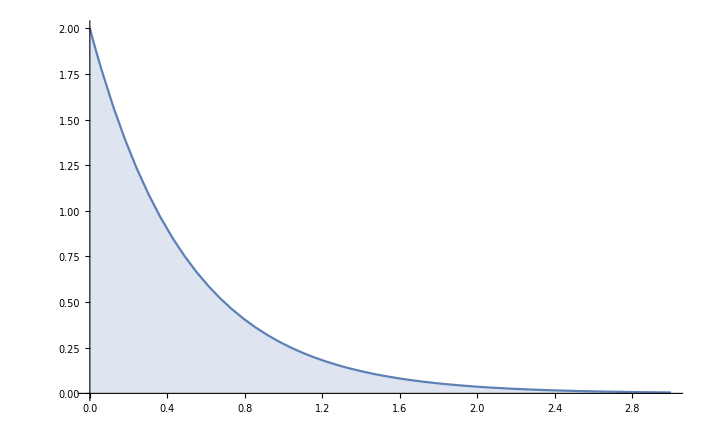

```mathematica
Plot[prior[μ],{μ,0,3},Filling->Axis]
```

#### Step 2 : let’s define our likelihood function of each data point as a Normal Distribution

An Normal distribution with mean 2 and variance 1/2 is

Since variance is 1/2, the corresponding standard deviation is

```mathematica
lf[x_]:=PDF[NormalDistribution[μ,1/Sqrt[2]],x]
```

```mathematica
lf[x]
```

(ⅇ^(-(x-μ)^2))/(√π)

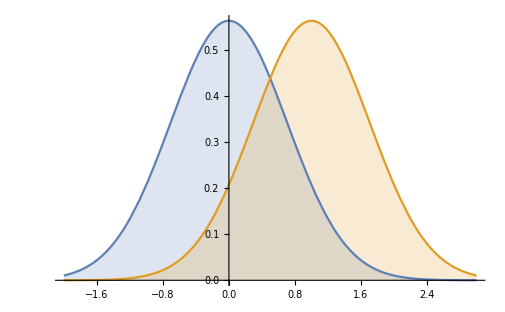

```mathematica
Plot[Table[lf[x],{μ,{0,1}}]//Evaluate,{x,-2,3},Filling->Axis]
```

#### Step 3 : let’s define our likelihood function of all data points as the product of Exponential PDFs

```mathematica
likelihood[f_,data_]:=Product[PDF[f,x],{x,data}]
```

```mathematica
likelihood[NormalDistribution[μ,1/Sqrt[2]],{Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[a, 5]}]
```

(ⅇ^(-(-μ+a_1)^2-(-μ+a_2)^2-(-μ+a_3)^2-(-μ+a_4)^2-(-μ+a_5)^2))/π^(5/2)

```mathematica
l = Simplify[likelihood[NormalDistribution[μ,1/Sqrt[2]],{Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[a, 5]}]]
```

(ⅇ^(-(μ-a_1)^2-(μ-a_2)^2-(μ-a_3)^2-(μ-a_4)^2-(μ-a_5)^2))/π^(5/2)

#### Step 4 : let’s calculate our posterior using Bayes Rule

The Bayes Rule suggests that

Since the denominator is just a constant, we just need to focus on the numerator calculation.
Let’s also assume

```mathematica
num = Assuming[μ>0,Simplify[l * prior[μ]]]
```

(2 ⅇ^(-2 μ-(μ-a_1)^2-(μ-a_2)^2-(μ-a_3)^2-(μ-a_4)^2-(μ-a_5)^2))/π^(5/2)

We don’t need to struggle with any constant terms; 
hence, let’s ignore  and  
just focus on the exponent of the exponential function.

```mathematica
s0 = Exponent[num,E]
```

-2 μ-(μ-a_1)^2-(μ-a_2)^2-(μ-a_3)^2-(μ-a_4)^2-(μ-a_5)^2

Again, we don’t need to struggle with any constant terms; 
hence, let’s 
1. expand the exponent

```mathematica
s1 =Expand[s0]
```

-2 μ-5 μ^2+2 μ a_1-a_1^2+2 μ a_2-a_2^2+2 μ a_3-a_3^2+2 μ a_4-a_4^2+2 μ a_5-a_5^2

2. remove all constant terms (terms without μ)

```mathematica
s2 = Collect[s1,μ]
```

-5 μ^2-a_1^2-a_2^2-a_3^2-a_4^2-a_5^2+μ (-2+2 a_1+2 a_2+2 a_3+2 a_4+2 a_5)

```mathematica
s3 = Select[s2,MemberQ[#,μ|μ^_]&]
```

-5 μ^2+μ (-2+2 a_1+2 a_2+2 a_3+2 a_4+2 a_5)

Hence, all the manipulations above can be summarized into the following operation

```mathematica
result = Select[Collect[Expand[Exponent[num,E]],μ],MemberQ[#,μ|μ^_]&]
```

-5 μ^2+μ (-2+2 a_1+2 a_2+2 a_3+2 a_4+2 a_5)

put the simplified exponent back to an expoential function, we have

```mathematica
Exp[result]
```

ⅇ^(-5 μ^2+μ (-2+2 a_1+2 a_2+2 a_3+2 a_4+2 a_5))

It looks like part of the Normal PDF

Let’s vary our sample points (add one extra sample points) to find the pattern of parameters.

```mathematica
l = Simplify[likelihood[NormalDistribution[μ,1/Sqrt[2]],{Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[a, 5],Subscript[a, 6]}]];
num = Assuming[μ>0,Simplify[l * prior[μ]]];
result = Select[Collect[Expand[Exponent[num,E]],μ],MemberQ[#,μ|μ^_]&]
```

-6 μ^2+μ (-2+2 a_1+2 a_2+2 a_3+2 a_4+2 a_5+2 a_6)

```mathematica
l = Simplify[likelihood[NormalDistribution[μ,1/Sqrt[2]],{Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],Subscript[a, 4]}]];
num = Assuming[μ>0,Simplify[l * prior[μ]]];
result = Select[Collect[Expand[Exponent[num,E]],μ],MemberQ[#,μ|μ^_]&]
```

-4 μ^2+μ (-2+2 a_1+2 a_2+2 a_3+2 a_4)

Hence, we know that the coefficient of  is the sample size n.
The final step is to rearrange  into a Normal PDF
We define  and replace the coefficient of  as sample size n.

```mathematica
p0 = E^(-n*( μ^2-2μ ( A-1/n)))
```

ⅇ^(-n (-2 (A-1/n) μ+μ^2))

```mathematica
p1 = E^(-n*( μ^2-2μ ( A-1/n)+(A-1/n)^2))
```

ⅇ^(-n ((A-1/n)^2-2 (A-1/n) μ+μ^2))

```mathematica
p2 = E^(-n*( μ-(A-1/n))^2)
```

ⅇ^(-n (-A+1/n+μ)^2)

Now you can see the posterior is 

which is a Normal distribution